## Integrate[x^-a (1-x)^4]

```mathematica
a=-0.16
Integrate[x^-a (1-x)^4,{x,0,1}]
Integrate[x^-0.16 (1-x)^4,{x,0,1}]
Integrate[x^0.16 (1-x)^4,{x,0,1}]
-24/((-5+a) (-4+a) (-3+a) (-2+a) (-1+a))
```

-0.16

0.141211

0.294184

0.141211

0.141211

## Integrate[x^-a (1-x)^5]

```mathematica
a=-0.16
Integrate[x^-a (1-x)^5,{x,0,1}]
120/((-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a))
```

-0.16

0.11462

0.11462

## Integrate[x^-a (1-x)^6]

```mathematica
a=-0.16
Integrate[x^-a (1-x)^6,{x,0,1}]
 -720/((-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a))
```

-0.16

0.0960499

0.0960499

## Integrate[x^-a (1-x)^b]

```mathematica
Integrate[x^-k (1-x)^m,{x,0,1}]
```

ConditionalExpression[(Gamma[1-k] Gamma[1+m])/Gamma[2-k+m],Re[k]<1&&Re[m]>-1]

```mathematica
mm[n_,a_,m_]:=n(Gamma[1-a] Gamma[1+b])/Gamma[2-a+b];
```

```mathematica
mm[1.,-0.16,4.]
```

0.11462

```mathematica
mm[9.3,0.16,5.0]
```

2.34239

```mathematica
a=-0.16
b=5
mm[1.,a,b]
```

-0.16

5

0.11462

```mathematica
normalization[a_,m_]:=(Gamma[1-a] Gamma[1+m])/Gamma[2-a+m];
patmm[nu_,a_,m_]:=nu*normalization[a,m];

nu=21.9901;
au=-0.157929;
mu=4;
Print["Normalization_u=",normalization[au,mu]];
Print["Proton Anomalous Magnetic Moment_u=",patmm[nu,au,mu]];


nd=9.29475;
ad=0.165366;
md=5;
Print["Normalization_d=",normalization[ad,md]];
Print["Proton Anomalous Magnetic Moment_d=",patmm[nd,ad,md]];
```

Normalization_u=0.14182

Proton Anomalous Magnetic Moment_u=3.11864

Normalization_d=0.255586

Proton Anomalous Magnetic Moment_d=2.37561

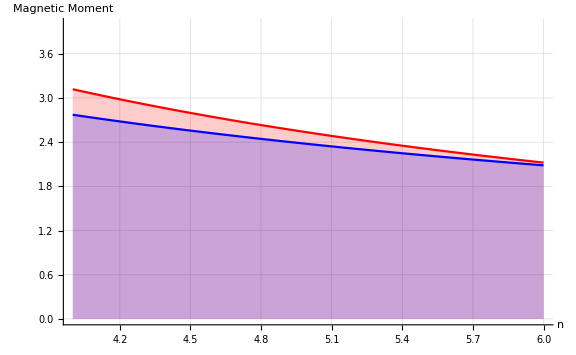

```mathematica
Plot[{patmm[nu,au,b],patmm[nd,ad,b]},{b,4,6},PlotRange->{All,{0,4}}, AxesLabel->{"n","Magnetic Moment"},GridLines->Automatic,Filling->Axis,ImageSize->Large,PlotStyle->{Red,Blue}]
```

```mathematica
slope[b_,a_,x_,t_]:=Exp[-(b-a Log[x])t]
```

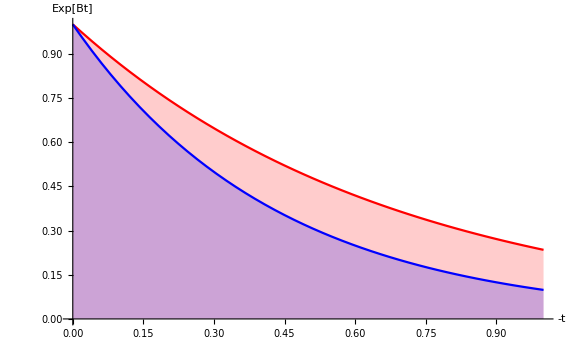

```mathematica
Plot[{slope[1.08,0.23,0.2,t],slope[0.,1.44,0.2,t]},{t,0.,1},Filling->Axis,ImageSize->Large,PlotStyle->{Red,Blue},AxesLabel->{"-t","Exp[Bt]"}]
```